## Iterative Arithmetic Functions

For the purposes of this notebook we model functions of the form φ(x)=a x^p+b where x∈ℤ. Although, we could expand the domain by making some easy changes. For now, however, let’s just look at this broad class of iterative arithmetic functions. To get started, see that we can define a function of this form either with an anonymous function:

```mathematica
Mod[#^2+1,11]&/@{0,1, 2, 3, 4}
```

{1,2,5,10,6}

Then, we can use the function NestList to generate a list of the function applied to itself for some amount of time given some initial value. There is the function NestListWhile that could iterate until some condition was met, but I couldn’t figure out how to get it too look if it had repeated itself. But I think there must be a way to be clever about finding an upper bound. But for now we’ll be blunt and choose the number 20. Here’s an example:

```mathematica
NestList[Mod[#^2+1,11]&,0,20]
```

{0,1,2,5,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4}

Now I want to feed bigram transitions into Mathematica’s GraphPlot funciton that needs a list of rules. We can do this using an offset on the Partition funciton. I define a the function function GetRules that takes in a list of numbers and spits out a list of transition rules:

```mathematica
GetRules[list_]:=Rule@@#&/@Partition[list,2,1]
GetRules[NestList[Mod[#^2+1,11]&,0,20]]
```

{0→1,1→2,2→5,5→4,4→6,6→4,4→6,6→4,4→6,6→4,4→6,6→4,4→6,6→4,4→6,6→4,4→6,6→4,4→6,6→4}

We also want to iterate over all reduced residues for a modulus q, i.e. get the rules for all of starting points in Range[0, q - 1]. Then we flatten the result to get a big list of rules. But, unfortunately this will have a lot of duplicates as rules does already! We can get rid of these with the Mathematica function DeleteDuplicates:

```mathematica
rules=DeleteDuplicates@Flatten[Map[GetRules,NestList[Mod[#^2+1,11]&,#,100]&/@Range[0,11-1]]]
```

{0→1,1→2,2→5,5→4,4→6,6→4,3→10,10→2,7→6,8→10,9→5}

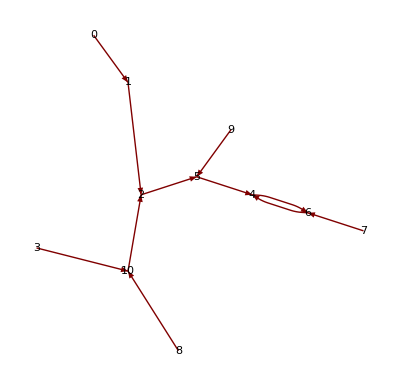

```mathematica
GraphPlot[rules,VertexLabeling->True,DirectedEdges->True]
```

For convenience, we create a function to do this for us:

```mathematica
GetPlot[f_,domain_,maxiter_]:=GraphPlot[DeleteDuplicates@Flatten[Map[GetRules,NestList[f,#,maxiter]&/@domain]],VertexLabeling->True]
```

And now let’s create a dynamic window for this funciton:

```mathematica
Manipulate[GetPlot[Mod[a#^p+b,q]&,Range[0,q-1],maxiter],{a,1,10,1,Appearance->"Labeled"},{b,1,10,1,Appearance->"Labeled"},{p,1,10,1,Appearance->"Labeled"},{q,2,15,1,Appearance->"Labeled"},{maxiter,10^2,10^4,1,Appearance->"Labeled"}]
```